```mathematica
(* Report And Work Data Generation GLOBALS *)
repFile="/Users/gediz/Desktop/LINEER SISTEMLERDE MODAL ENERJI HESABI.pdf";
datFile="/Users/gediz/Desktop/LINEER SISTEMLERDE MODAL ENERJI HESABI-Data.dat";
LogOut=ConstantArray[0,1000];
outCnt=0;

TraditionallyFormattedOutput[x_,str_]:=(
outCnt++;
LogOut[[outCnt]]=Text[TraditionalForm[str]];
outCnt++;outCnt++;LogOut[[outCnt]]="";LogOut[[outCnt-1]]=TraditionalForm[x]//MatrixForm
)

TFO=TraditionallyFormattedOutput;
HFO=HoldForm;

(* TFO[HFO[Us2=Us/Sqrt[Us.M.Us]],"Mass Nomalization Formula"]
TFO[Um2,"Mass Normalized EigenVectors"]

Table[LogOut[[i]]//TraditionalForm,{i,1,outCnt}]//MatrixForm //TraditionalForm
Export[repFile,%//MatrixForm]; *)
```

```mathematica
TFO["SYSTEM ON ENERGY EQUAPARTITION PAPER IS EXPLAINED ON 3 DOF EXAMPLE SYSTEM","FORMATTED REPORT 1"]
```

SYSTEM ON ENERGY EQUAPARTITION PAPER IS EXPLAINED ON 3 DOF EXAMPLE SYSTEM

```mathematica
TFO["SETTING SYSTEM ATTRIBUTES AND CONSTRUCTION OF MASS AND STIFNESS MATRICES","PART 1-ANALYTIC"]
n=2;
Subscript[k, 1]=K;
Subscript[m, 1]=M;
Km=DiagonalMatrix[Table[Subscript[k, j],{j,1,n+1}]];
Mm=DiagonalMatrix[Table[Subscript[m, j],{j,1,n+1}]];
For[j=2,j<n+2,j++,Km[[1,j]]=-Subscript[k, j];Km[[j,1]]=-Subscript[k, j];];Clear[j];
Km[[1,1]]=Sum[Subscript[k, i],{i,1,n+1}];

TFO[Mm,"Mass Matrix"]
TFO[Km, "Stiffness Matrix"]
```

SETTING SYSTEM ATTRIBUTES AND CONSTRUCTION OF MASS AND STIFNESS MATRICES

(M | 0 | 0
0 | m_2 | 0
0 | 0 | m_3)

(K+k_2+k_3 | -k_2 | -k_3
-k_2 | k_2 | 0
-k_3 | 0 | k_3)

```mathematica
TFO["DEFINING MODAL PLANE MATRICES AND VARIABLES","PART 2-ANALYTIC"]


Um=Table[Subscript[U, i,j],{i,1,n+1},{j,1,n+1}] ;
xm=Table[Subscript[x, i],{i,1,n+1}];
ηm=Table[Subscript[η, i],{i,1,n+1}];
(*{xm//MatrixForm,(Um.ηm)//MatrixForm};*)
Table[Subscript[η, i]=Subscript[C, i] Cos[Subscript[ω, i] t-Subscript[ψ, i]],{i,1,n+1}];
(*{xm//MatrixForm,(Um.ηm)//MatrixForm};*)
xm2=Um.ηm;
(* Ψm=Inverse[Um];*)
Zeros=ConstantArray[0,n+1];


TFO[Um,"EigenVectors, Transformation Matrix"]
TFO[xm//MatrixForm,"Generalized Coordinates"]
TFO[ηm//MatrixForm,"Modal Coodrinates"]
TFO[HFO[xm=Um.ηm],"Transition To Modal Coordinates"]
TFO[xm2//MatrixForm,"Displacement Matrix in Modal Plane"]
```

DEFINING MODAL PLANE MATRICES AND VARIABLES

(U_(1,1) | U_(1,2) | U_(1,3)
U_(2,1) | U_(2,2) | U_(2,3)
U_(3,1) | U_(3,2) | U_(3,3))

(x_1
x_2
x_3)

(C_1 cos(ψ_1-t ω_1)
C_2 cos(ψ_2-t ω_2)
C_3 cos(ψ_3-t ω_3))

xm=Um.ηm

(C_1 U_(1,1) cos(ψ_1-t ω_1)+C_2 U_(1,2) cos(ψ_2-t ω_2)+C_3 U_(1,3) cos(ψ_3-t ω_3)
C_1 U_(2,1) cos(ψ_1-t ω_1)+C_2 U_(2,2) cos(ψ_2-t ω_2)+C_3 U_(2,3) cos(ψ_3-t ω_3)
C_1 U_(3,1) cos(ψ_1-t ω_1)+C_2 U_(3,2) cos(ψ_2-t ω_2)+C_3 U_(3,3) cos(ψ_3-t ω_3))

```mathematica
TFO["CALCULATION OF ENERGIES","PART 3-ANALYTIC"]


EKinN=1/2*M*D[xm2[[1]],t]^2  ;  (*Master Kinetik Enerji*)
EPotN=1/2*K*xm2[[1]]^2  ;                (*Master Potansiyel Enerji*)
EKinm=Table[1/2*Mm[[i,i]]*D[xm2[[i]],t]^2,{i,2,n+1}] ; (*Satellite Kinetik Enerji*)
EPotm=Table[1/2*Km[[i,i]]*(xm2[[i]]-xm2[[1]])^2,{i,2,n+1}];  (*Sattelite Pot. Enerji*)
Etop1=EKinN+EPotN+Total[EKinm]+Total[EPotm]; (*Toplam Enerji*)
Etop2=1/2*xm2.Km.xm2+1/2*D[xm2,t].Mm.D[xm2,t] ;(*Toplam Enerji Quadratik Form*)



TFO[HFO[EKinN=1/2*M*D[xm2[[1]],t]^2 ] , "Kinetic Energy of Master"]
TFO[HFO[EPotN=1/2*K*xm2[[1]]^2 ] , "Potential Energy of Master"]

TFO[HFO[EKinm=Table[1/2*Mm[[i,i]]*D[xm2[[i]],t]^2,{i,2,n+1}]],"Kinetic Energy Of Sattelites"]
TFO[HFO[EPotm=Table[1/2*Km[[i,i]]*(xm2[[i]]-xm2[[1]])^2,{i,2,n+1}]],  "Potential Energy Of Sattalites"]
TFO[HFO[Etop1=EKinN+EPotN+Total[EKinm]+Total[EPotm]],"Total Energy by means of summing Total Kin.&Pot. Energy"]
TFO[HFO[Etop2=1/2*xm2.Km.xm2+1/2*D[xm2,t].Mm.D[xm2,t] ],"Total Energy in Quadratic Form"]

TFO[HFO[Simplify[Etop1-Etop2]],"SAGLAMA ETOPsum-ETOPQuadratik=0"]
TFO[Simplify[Etop1-Etop2],"Etop1-Etop2"]
```

CALCULATION OF ENERGIES

EKinN=1/2 M ((∂xm2⟦1⟧)/(∂t))^2

EPotN=1/2 K xm2⟦1⟧^2

EKinm=Table[1/2 Mm⟦i,i⟧ ((∂xm2⟦i⟧)/(∂t))^2,{i,2,n+1}]

EPotm=Table[1/2 Km⟦i,i⟧ (xm2⟦i⟧-xm2⟦1⟧)^2,{i,2,n+1}]

Etop1=EKinN+EPotN+Total[EKinm]+Total[EPotm]

Etop2=(xm2.Km.xm2)/2+1/2 (∂xm2)/(∂t).Mm.(∂xm2)/(∂t)

Simplify[Etop1-Etop2]

0

```mathematica
TFO ["MODAL ENERGY CALCULATIONS", "PART 4-ANALYTIC"]

EtotImp=1/2*M*V0^2;
ωm=Zeros;
Table[ωm[[i]]=Subscript[ω, i],{i,1,n+1}];
EModal=ConstantArray[0,n+1];
EModal3=ConstantArray[Zeros,n+1];
EModal=Table[1/2*(ωm[[i]]^2*ηm[[j]]^2+D[ηm[[j]],t]^2),{i,1,n+1},{j,1,n+1}] ;
EModal=Simplify[EModal];
EModal3=Table[M*EtotImp*Um[[i,j]] ^2,{j,1,n+1},{i,1,n+1}];

TFO[HFO[EtotImp=1/2*M*V0^2],"Total Energy Imparted to Master"]
TFO[ωm//MatrixForm,"Natural Modes (Frequencies) of System"]
TFO[HFO[EModal=Table[1/2*(ωm[[i]]^2*ηm[[j]]^2+D[ηm[[i]],t]^2),{i,1,n+1},{j,1,n+1}] ],"Modal Energy Form 1"]
TFO[EModal,"Modal Energy Form 1 Expanded"]
TFO[HFO[EModal3=Table[M*EtotImp*Um[[i,j]] ^2,{j,1,n+1},{i,1,n+1}]],"Modal Energy Form 3"]
TFO[EModal3,"Modal Energy Form 3 Expanded"]
TFO["Note that Modal Energy Form 2 will be given after"," numerical values are introduced"]
```

MODAL ENERGY CALCULATIONS

EtotImp=(M V0^2)/2

(ω_1
ω_2
ω_3)

EModal=Table[1/2 (ωm⟦i⟧^2 ηm⟦j⟧^2+((∂ηm⟦i⟧)/(∂t))^2),{i,1,n+1},{j,1,n+1}]

(1/2 C_1^2 ω_1^2 | 1/2 C_2^2 (cos^2(ψ_2-t ω_2) ω_1^2+sin^2(ψ_2-t ω_2) ω_2^2) | 1/2 C_3^2 (cos^2(ψ_3-t ω_3) ω_1^2+sin^2(ψ_3-t ω_3) ω_3^2)
1/2 C_1^2 (sin^2(ψ_1-t ω_1) ω_1^2+cos^2(ψ_1-t ω_1) ω_2^2) | 1/2 C_2^2 ω_2^2 | 1/2 C_3^2 (cos^2(ψ_3-t ω_3) ω_2^2+sin^2(ψ_3-t ω_3) ω_3^2)
1/2 C_1^2 (sin^2(ψ_1-t ω_1) ω_1^2+cos^2(ψ_1-t ω_1) ω_3^2) | 1/2 C_2^2 (sin^2(ψ_2-t ω_2) ω_2^2+cos^2(ψ_2-t ω_2) ω_3^2) | 1/2 C_3^2 ω_3^2)

EModal3=Table[M EtotImp Um⟦i,j⟧^2,{j,1,n+1},{i,1,n+1}]

(1/2 M^2 V0^2 U_(1,1)^2 | 1/2 M^2 V0^2 U_(2,1)^2 | 1/2 M^2 V0^2 U_(3,1)^2
1/2 M^2 V0^2 U_(1,2)^2 | 1/2 M^2 V0^2 U_(2,2)^2 | 1/2 M^2 V0^2 U_(3,2)^2
1/2 M^2 V0^2 U_(1,3)^2 | 1/2 M^2 V0^2 U_(2,3)^2 | 1/2 M^2 V0^2 U_(3,3)^2)

Note that Modal Energy Form 2 will be given after

```mathematica
TFO["DERIVATION OF EQUATIONS OF MOTION USING LAGRANGIAN MECHANICS (including NonLineer Eq.)","PART5-ANALYTIC"];

Subscript[F, yay][x_,k_]=k*x[t];
IFk=Integrate[Subscript[F, yay][x,k],x[t]];
T =0.5* M *Subscript[x, 1]'[t]^2 + 0.5*Sum[Subscript[m, i]*D[Subscript[x, i][t],t]^2, {i,2,n+1}];
V1=IFk/.{x[t]->Subscript[x, 1][t],k->K};
V2=Sum[IFk/.{x[t]->Subscript[x, i][t]-Subscript[x, 1][t],k->Subscript[k, i]},{i, 2, n+1}];
V=V1+V2;
L=T-V;
Eqs=Table[ D[L,Subscript[x, i][t]]-D[D[L,D[Subscript[x, i][t],t]],t]==0 , {i,1,n+1} ];
AllVars=Table[Subscript[x, i],{i,1,n+1}];
InitialCon=Flatten[{Table[Subscript[x, i][0]==0,{i,1,n+1}],Table[Subscript[x, i]'[0]==0,{i,2,n+1}],Subscript[x, 1]'[0]==1}];

TFO[HFO[Subscript[F, yay][x_,k_]=k*x[t]],"Spring Force For all springs"]

TFO[HFO[{IFk=Integrate[Subscript[F, yay][x,k],x[t]];
T =0.5* M *Subscript[x, 1]'[t]^2 + 0.5*Sum[Subscript[m, i]*D[Subscript[x, i][t],t]^2, {i,2,n+1}];
V1=IFk/.{x[t]->Subscript[x, 1][t],k->K};
V2=Sum[IFk/.{x[t]->Subscript[x, i][t]-Subscript[x, 1][t],k->Subscript[k, i]},{i, 2, n+1}];
V=V1+V2;}]//MatrixForm,"Calculations Inbetween"]

TFO[HFO[L=T-V],"Lagrangian Equation"]

TFO[HFO[Eqs=Table[ D[L,Subscript[x, i][t]]-D[D[L,D[Subscript[x, i][t],t]],t]==0 , {i,1,n+1} ]],"Euler-Lagrange Function"]
TFO[Eqs//MatrixForm,"Equations of Motions"]
TFO[InitialCon//MatrixForm,"Initial Conditions"]
```

F_yay(x_,k_)=k x(t)

{IFk=∫F_yay(x,k)ⅆx(t);T=0.5 M ((x_1)'(t))^2+0.5 ∑_(i=2)^(n+1) m_i ((∂x_i(t))/(∂t))^2;V1=IFk/.{x(t)→x_1(t),k→K};V2=∑_(i=2)^(n+1) (IFk/.{x(t)→x_i(t)-x_1(t),k→k_i});V=V1+V2;}

L=T-V

Eqs=Table[(∂L)/(∂x_i(t))-∂/(∂t)(∂L)/(∂(∂x_i(t))/(∂t))==0,{i,1,n+1}]

(-1. M (x_1)''(t)+k_2 (x_2(t)-x_1(t))+k_3 (x_3(t)-x_1(t))-K x_1(t)==0
-1. m_2 (x_2)''(t)-k_2 (x_2(t)-x_1(t))==0
-1. m_3 (x_3)''(t)-k_3 (x_3(t)-x_1(t))==0)

(x_1(0)==0
x_2(0)==0
x_3(0)==0
(x_2)'(0)==0
(x_3)'(0)==0
(x_1)'(0)==1)

INTRODUCING NUMERICAL VALUES AND CALCULATE SYSTEM NUMERICALLY

{1,1.152,1.40404}

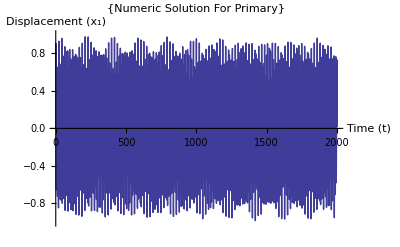

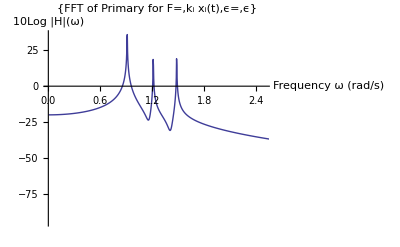

```mathematica
TFO ["INTRODUCING NUMERICAL VALUES AND CALCULATE SYSTEM NUMERICALLY","PART 6"]
Subscript[ω, 1]=Sqrt[K/M];
TIME=2000;
dt=10;
df=0.1;

M=1;
K=1;
Subscript[V, 1]=1;
V0=Subscript[V, 1];

For[i=2,i<n+2,++i,Subscript[m, i]=0.1/n]
For[i=2,i<n+2,++i,Subscript[k, i]=Subscript[m, i]*Subscript[ω, i]^2]
For[i=2,i<n+2,++i,Subscript[ω, i]=0.77+0.65*5*Sin[π/20/n*i-π/40/n]];
Clear[i];
Ωr=Table[Subscript[ω, i],{i,1,n+1}];

(*Degerler atandiktan hemen sonra Numerik Cozum*)
numsol=NDSolve[Flatten[Join[Eqs,InitialCon]],AllVars,{t,0,TIME},MaxSteps->∞,PrecisionGoal->12,AccuracyGoal->12];

Plot1=Plot[
Evaluate[Subscript[x, 1][t]/.numsol],{t,0,TIME},
PlotRange->{{0,TIME},{-1,1}},
PlotLabel->{"Numeric Solution For Primary"},
AxesLabel->{"Time (t)","Displacement (x_1)"} ,
ImageSize->Scaled[0.35]];

a=Abs[Fourier[Table[(Subscript[x, 1]/.numsol[[1]])[i*df],{i,0,TIME/df}]]];
b=Table[{N[i/TIME*2π],10*Log[a[[i]]]},{i,1,TIME/df}];
Plot2=ListLinePlot[b,PlotRange->{{0,2.5},All} ,PlotLabel->{"FFT of Primary for F=",Subscript[F, yay][Subscript[x, i],Subscript[k, i]], "ϵ=",ϵ},AxesLabel->{"Frequency ω (rad/s)","10Log |H|(ω)"},ImageSize->Scaled[0.35]];
Clear[a,b];


TFO[Ωr,"Independent Frequencies of Primary And Sattalites"]
TFO[Plot1,"Numerically Solved Displacement Of Primary"]
TFO[Plot2,"FFT of Displacement of Primary"]
```

```mathematica
TFO ["EigenSystem and Analytic Solution Both using a Symbolic Solver and a Modal Analysis Technique","PART 7"] 
eigsys=Eigensystem[{Km,Mm}];
eigs=Reverse[eigsys[[1]]];
eigvecs=Transpose[Reverse[eigsys[[2]]]];


Um=eigvecs;
Ωm=Table[Subscript[ω, i]=Sqrt[ eigs[[i]] ] ,{i,1,n+1}];
Table[Subscript[U, i,j]=eigvecs[[i,j]],{i,1,n+1},{j,1,n+1}];

(* Modal Enerji 2. ifade *)
Ψm=Inverse[Um];
EModal2=Table[V0^2*Ψm[[i,j]] ^2/2,{j,1,n+1},{i,1,n+1}];

(*ic={ConstantArray[0,n+1],ConstantArray[0,n+1]};
ic[[2,1]]=1;
ic//MatrixForm;
Clear[Eqs];
Eqs=Flatten[Table[{xm2[[i]]==ic[[1,i]],D[xm2[[i]],t]==ic[[2,i]] },{i,1,n+1}]];
Solvars=Flatten[Table[{Subscript[ψ, i],Subscript[C, i]},{i,1,n+1}]];
Timing[AnSolCoeffs=Solve[Eqs/.t->0,Solvars]];
Table[{Subscript[ψ, i]=Subscript[ψ, i]/.AnSolCoeffs[[1]],Subscript[C, i]=Subscript[C, i]/.AnSolCoeffs[[1]]},{i,1,n+1}];
*)

TFO[Um,"Modal Transformation Matrix (EigenVectors) using EigenSolution"]
TFO[Ωm,"Natural Modes (EigenFrequencies) using EigenSolution"]
TFO[HFO[Ψm=Inverse[Um]],"Inverse of EigenVectors"]
TFO[Ωm,"Inverse of EigenVectors"]
TFO[HFO[EModal2=Table[V0^2*Ψm[[i,j]] ^2/2,{j,1,n+1},{i,1,n+1}]],"Calculation of Modal Energy Form 2"]
TFO[EModal2,"Modal Energy Form 2"]
```

EigenSystem and Analytic Solution Both using a Symbolic Solver and a Modal Analysis Technique

(-0.303802 | -0.0919473 | -0.105573
-0.797705 | 0.931015 | 0.163593
-0.520934 | -0.35321 | 0.980863)

{0.906464,1.20754,1.47767}

Ψm=Um

{0.906464,1.20754,1.47767}

EModal2=Table[1/2 V0^2 Ψm⟦i,j⟧^2,{j,1,n+1},{i,1,n+1}]

(2.43447 | 1.25522 | 1.51808
0.041961 | 0.321732 | 0.00911305
0.0178948 | 0.0463069 | 0.327604)

ENERGY PLOTS and CALCULATIONS AFTER NUMERICAL SOLUTION

Uydu Kutlelerin Toplam Enerji Gecislerinin Cizdirilmesi

-Graphics3D-

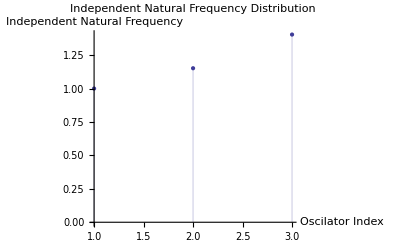

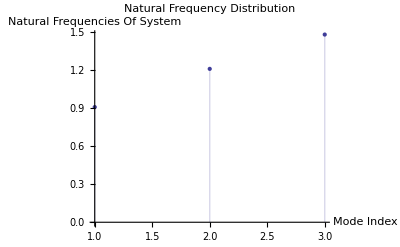

-Graphics-

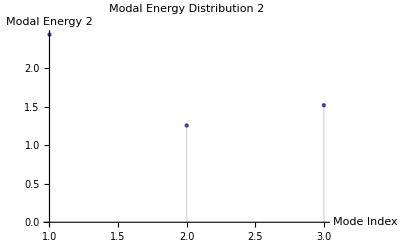

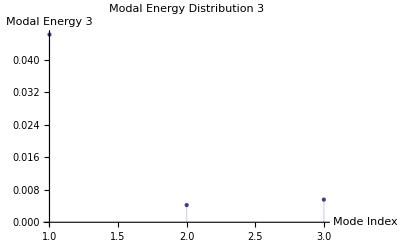

-Graphics3D-

MODAL ENERJI IFADELERININ SONUCLARI

{{0.410839 C_1^2,1/2 (0.821678 Cos[1.20754 t-ψ_2]^2+1.45816 Sin[1.20754 t-ψ_2]^2) C_2^2,1/2 (0.821678 Cos[1.47767 t-ψ_3]^2+2.18352 Sin[1.47767 t-ψ_3]^2) C_3^2},{1/2 (1.45816 Cos[0.906464 t-ψ_1]^2+0.821678 Sin[0.906464 t-ψ_1]^2) C_1^2,0.72908 C_2^2,1/2 (1.45816 Cos[1.47767 t-ψ_3]^2+2.18352 Sin[1.47767 t-ψ_3]^2) C_3^2},{1/2 (2.18352 Cos[0.906464 t-ψ_1]^2+0.821678 Sin[0.906464 t-ψ_1]^2) C_1^2,1/2 (2.18352 Cos[1.20754 t-ψ_2]^2+1.45816 Sin[1.20754 t-ψ_2]^2) C_2^2,1.09176 C_3^2}}

{{2.43447,1.25522,1.51808},{0.041961,0.321732,0.00911305},{0.0178948,0.0463069,0.327604}}

{{0.0461479,0.318166,0.135686},{0.00422716,0.433394,0.0623785},{0.00557278,0.0133814,0.481046}}

```mathematica
TFO["ENERGY PLOTS and CALCULATIONS AFTER NUMERICAL SOLUTION","PART X"]
TFO["Uydu Kutlelerin Toplam Enerji Gecislerinin Cizdirilmesi ",""]

dt=10;
Subscript[m, 1]=M;
Subscript[k, 1]=K;
Clear[i];
ETOP[t_,i_]=1/2*(Subscript[m, i]*D[Subscript[x, i][t],t]^2+Subscript[k, i]*(Subscript[x, i][t]-Subscript[x, 1][t])^2);
(*HINT NUMERIK SOLUTIONDAN CEK*)ETOP[3,2]/.numsol;
EPRIM=1/2*(M*D[Subscript[x, 1][t],t]^2+K*Subscript[x, 1][t]^2);
n;
data=Table[(ETOP[j*dt,i]/.numsol)[[1]] ,{i,2,n+1},{j,0,TIME/dt}];
data2=Table[EModal3[[i,j]],{i,1,n+1},{j,1,n+1}];

TFO[
ListPlot3D[data,
Mesh->None,
InterpolationOrder->3,
ColorFunction->"SouthwestColors",
PlotRange->All,
PlotLabel->{"OverTime Energy Transition between Satellites"},
AxesLabel->{"Time (t)","Satellite index","Total Energy of Indexed Sattelite"},
ImageSize->Scaled[0.4]]
,"OverTime Energy Transition between Satellites"]

TFO[DiscretePlot[Ωr[[i]],{i,1,n+1},PlotRange->All,AxesLabel->{"Oscilator Index","Independent Natural Frequency"},PlotLabel->"Independent Natural Frequency Distribution"],"Independent Natural Frequency Distribution"]
TFO[DiscretePlot[Ωm[[i]],{i,1,n+1},PlotRange->All,AxesLabel->{"Mode Index","Natural Frequencies Of System"},PlotLabel->"Natural Frequency Distribution"],"Natural Frequency Distribution"]
TFO[DiscretePlot[EModal[[i]],{i,1,n+1},PlotRange->All,AxesLabel->{"Mode Index","Modal Energy 3"},PlotLabel->"Modal Energy Distribution 1"],"Modal Energy Distribution 1"]
TFO[DiscretePlot[EModal2[[1,i]],{i,1,n+1},PlotRange->All,AxesLabel->{"Mode Index","Modal Energy 2"},PlotLabel->"Modal Energy Distribution 2"],"Modal Energy Distribution 2"]
TFO[DiscretePlot[EModal3[[i,1]],{i,1,n+1},PlotRange->All,AxesLabel->{"Mode Index","Modal Energy 3"},PlotLabel->"Modal Energy Distribution 3"], "Modal Energy Distribution 3"]
TFO[ListPointPlot3D[data2,
ColorFunction->"SouthwestColors",
PlotRange->All,
PlotLabel->{"Modal Energy Distribution for each Mass"},
AxesLabel->{"Mode index","Mass index","Modal Energy"},
ImageSize->Scaled[0.4]],"Modal Energy Distribution 3 For Each Mass"
]

"MODAL ENERJI IFADELERININ SONUCLARI"
EModal
EModal2
EModal3
```

(FORMATTED REPORT 1
SYSTEM ON ENERGY EQUAPARTITION PAPER IS EXPLAINED ON 3 DOF EXAMPLE SYSTEM

PART 1-ANALYTIC
SETTING SYSTEM ATTRIBUTES AND CONSTRUCTION OF MASS AND STIFNESS MATRICES

Mass Matrix
(1 | 0 | 0
0 | 0.05 | 0
0 | 0 | 0.05)

Stiffness Matrix
(1.18208 | -0.072908 | -0.109176
-0.072908 | 0.072908 | 0
-0.109176 | 0 | 0.109176)

PART 2-ANALYTIC
DEFINING MODAL PLANE MATRICES AND VARIABLES

EigenVectors, Transformation Matrix
(-0.303802 | -0.0919473 | -0.105573
-0.797705 | 0.931015 | 0.163593
-0.520934 | -0.35321 | 0.980863)

Generalized Coordinates
(x_1
x_2
x_3)

Modal Coodrinates
(cos(0.906464 t-ψ_1) C_1
cos(1.20754 t-ψ_2) C_2
cos(1.47767 t-ψ_3) C_3)

Transition To Modal Coordinates
xm=Um.ηm

Displacement Matrix in Modal Plane
(-0.303802 cos(0.906464 t-ψ_1) C_1-0.0919473 cos(1.20754 t-ψ_2) C_2-0.105573 cos(1.47767 t-ψ_3) C_3
-0.797705 cos(0.906464 t-ψ_1) C_1+0.931015 cos(1.20754 t-ψ_2) C_2+0.163593 cos(1.47767 t-ψ_3) C_3
-0.520934 cos(0.906464 t-ψ_1) C_1-0.35321 cos(1.20754 t-ψ_2) C_2+0.980863 cos(1.47767 t-ψ_3) C_3)

PART 3-ANALYTIC
CALCULATION OF ENERGIES

Kinetic Energy of Master
EKinN=1/2 M ((∂xm2⟦1⟧)/(∂t))^2

Potential Energy of Master
EPotN=1/2 K xm2⟦1⟧^2

Kinetic Energy Of Sattelites
EKinm=Table[1/2 Mm⟦i,i⟧ ((∂xm2⟦i⟧)/(∂t))^2,{i,2,n+1}]

Potential Energy Of Sattalites
EPotm=Table[1/2 Km⟦i,i⟧ (xm2⟦i⟧-xm2⟦1⟧)^2,{i,2,n+1}]

Total Energy by means of summing Total Kin.&Pot. Energy
Etop1=EKinN+EPotN+Total[EKinm]+Total[EPotm]

Total Energy in Quadratic Form
Etop2=(xm2.Km.xm2)/2+1/2 (∂xm2)/(∂t).Mm.(∂xm2)/(∂t)

SAGLAMA ETOPsum-ETOPQuadratik=0
Simplify[Etop1-Etop2]

Etop1-Etop2
0

PART 4-ANALYTIC
MODAL ENERGY CALCULATIONS

Total Energy Imparted to Master
EtotImp=(M V0^2)/2

Natural Modes (Frequencies) of System
(0.906464
1.20754
1.47767)

Modal Energy Form 1
EModal=Table[1/2 (ωm⟦i⟧^2 ηm⟦j⟧^2+((∂ηm⟦i⟧)/(∂t))^2),{i,1,n+1},{j,1,n+1}]

Modal Energy Form 1 Expanded
(0.410839 C_1^2 | 1/2 (0.821678 cos^2(1.20754 t-ψ_2)+1.45816 sin^2(1.20754 t-ψ_2)) C_2^2 | 1/2 (0.821678 cos^2(1.47767 t-ψ_3)+2.18352 sin^2(1.47767 t-ψ_3)) C_3^2
1/2 (1.45816 cos^2(0.906464 t-ψ_1)+0.821678 sin^2(0.906464 t-ψ_1)) C_1^2 | 0.72908 C_2^2 | 1/2 (1.45816 cos^2(1.47767 t-ψ_3)+2.18352 sin^2(1.47767 t-ψ_3)) C_3^2
1/2 (2.18352 cos^2(0.906464 t-ψ_1)+0.821678 sin^2(0.906464 t-ψ_1)) C_1^2 | 1/2 (2.18352 cos^2(1.20754 t-ψ_2)+1.45816 sin^2(1.20754 t-ψ_2)) C_2^2 | 1.09176 C_3^2)

Modal Energy Form 3
EModal3=Table[M EtotImp Um⟦i,j⟧^2,{j,1,n+1},{i,1,n+1}]
)

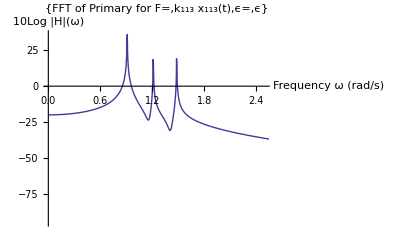
(
Modal Energy Form 3 Expanded
(0.0461479 | 0.318166 | 0.135686
0.00422716 | 0.433394 | 0.0623785
0.00557278 | 0.0133814 | 0.481046)

 numerical values are introduced
Note that Modal Energy Form 2 will be given after

PART5-ANALYTIC
DERIVATION OF EQUATIONS OF MOTION USING LAGRANGIAN MECHANICS (including NonLineer Eq.)

Spring Force For all springs
F_yay(x_,k_)=k x(t)

Calculations Inbetween
{IFk=∫F_yay(x,k)ⅆx(t);T=0.5 M ((x_1)'(t))^2+0.5 ∑_(i=2)^(n+1) m_i ((∂x_i(t))/(∂t))^2;V1=IFk/.{x(t)→x_1(t),k→K};V2=∑_(i=2)^(n+1) (IFk/.{x(t)→x_i(t)-x_1(t),k→k_i});V=V1+V2;}

Lagrangian Equation
L=T-V

Euler-Lagrange Function
Eqs=Table[(∂L)/(∂x_i(t))-∂/(∂t)(∂L)/(∂(∂x_i(t))/(∂t))==0,{i,1,n+1}]

Equations of Motions
(-x_1(t)+0.072908 (x_2(t)-x_1(t))+0.109176 (x_3(t)-x_1(t))-1. (x_1)''(t)==0
-0.072908 (x_2(t)-x_1(t))-0.05 (x_2)''(t)==0
-0.109176 (x_3(t)-x_1(t))-0.05 (x_3)''(t)==0)

Initial Conditions
(x_1(0)==0
x_2(0)==0
x_3(0)==0
(x_2)'(0)==0
(x_3)'(0)==0
(x_1)'(0)==1)

PART 6
INTRODUCING NUMERICAL VALUES AND CALCULATE SYSTEM NUMERICALLY

Independent Frequencies of Primary And Sattalites
{1,1.152,1.40404}

Numerically Solved Displacement Of Primary
-Graphics-

FFT of Displacement of Primary
-Graphics-

PART 7
EigenSystem and Analytic Solution Both using a Symbolic Solver and a Modal Analysis Technique

Modal Transformation Matrix (EigenVectors) using EigenSolution
(-0.303802 | -0.0919473 | -0.105573
-0.797705 | 0.931015 | 0.163593
-0.520934 | -0.35321 | 0.980863)

Natural Modes (EigenFrequencies) using EigenSolution
{0.906464,1.20754,1.47767}

Inverse of EigenVectors
Ψm=Um

Inverse of EigenVectors
{0.906464,1.20754,1.47767}

Calculation of Modal Energy Form 2
EModal2=Table[1/2 V0^2 Ψm⟦i,j⟧^2,{j,1,n+1},{i,1,n+1}]

Modal Energy Form 2
(2.43447 | 1.25522 | 1.51808
0.041961 | 0.321732 | 0.00911305
0.0178948 | 0.0463069 | 0.327604)

PART X
ENERGY PLOTS and CALCULATIONS AFTER NUMERICAL SOLUTION


Uydu Kutlelerin Toplam Enerji Gecislerinin Cizdirilmesi 

OverTime Energy Transition between Satellites
-Graphics3D-

Independent Natural Frequency Distribution
-Graphics-

Natural Frequency Distribution
-Graphics-
)

```mathematica
Table[LogOut[[i]]//TraditionalForm,{i,1,outCnt}]//MatrixForm //TraditionalForm
Export[repFile,%//MatrixForm//TraditionalForm]
```